## Is Morpho doing what it says it’s doing? Sanity check for penetration depth: Twist Profile as measured on the x-axis

### K = 1, C = 2, q = 1,2,3

```mathematica
NzC2q1={{0,0.998331},{0.0561336,0.997755},{0.112267,0.994313},{0.168401,0.989829},{0.224534,0.983227},{0.280668,0.97413},{0.336802,0.962641},{0.392935,0.945932},{0.449069,0.926049},{0.505202,0.911277},{0.561336,0.865244},{0.61747,0.859164},{0.673603,0.793368},{0.729737,0.761274},{0.78587,0.712074},{0.842004,0.662259},{0.898138,0.589847},{0.954271,0.504712},{1.0104,0.418697},{1.06654,0.318527}};
NzC2q2 = {{0,0.999403},{0.0549918,0.998779},{0.109984,0.996154},{0.164975,0.992481},{0.219967,0.987045},{0.274959,0.979553},{0.329951,0.969885},{0.384943,0.957649},{0.439935,0.941278},{0.494926,0.919974},{0.549918,0.893642},{0.60491,0.861072},{0.659902,0.823061},{0.714894,0.763155},{0.769885,0.696932},{0.824877,0.616903},{0.879869,0.526411},{0.934861,0.426022},{0.989853,0.300529},{1.04484,0.199377}};
NzC2q3={{0,0.999527},{0.0540129,0.999018},{0.108026,0.996929},{0.162039,0.993989},{0.216052,0.989581},{0.270065,0.981798},{0.324078,0.971707},{0.378091,0.958237},{0.432104,0.939316},{0.486116,0.915091},{0.540129,0.887068},{0.594142,0.85299},{0.648155,0.814122},{0.702168,0.76698},{0.756181,0.701012},{0.810194,0.600687},{0.864207,0.488565},{0.91822,0.367275},{0.972233,0.223735},{1.02625,0.065566}};
```

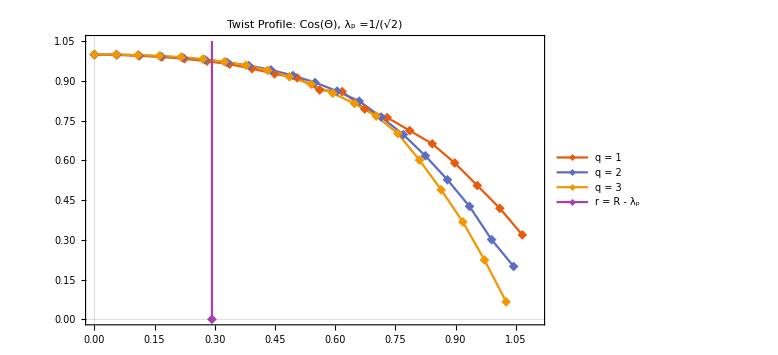

```mathematica
ListLinePlot[{NzC2q1,NzC2q2,NzC2q3,{{1-1/Sqrt[2],0},{1-1/Sqrt[2],1.5}}},PlotTheme->"Scientific", PlotLabel->"Twist Profile: Cos(Θ), λ_p =1/(√2)", PlotMarkers->{"◆", 10},PlotRange->{{0,1.1},{0.0,1.05}},PlotLegends->{"q = 1","q = 2","q = 3","r = R - λ_p"},ImageSize->Large]
```

### K = 1, C = 5 q = 1,2,3

```mathematica
NzC5q1={{0,0.999632},{0.056138,0.999264},{0.112276,0.997689},{0.168414,0.995448},{0.224552,0.992228},{0.28069,0.987808},{0.336828,0.981841},{0.392966,0.974219},{0.449104,0.964653},{0.505242,0.952319},{0.56138,0.93521},{0.617518,0.913521},{0.673656,0.889751},{0.729794,0.854028},{0.785932,0.811373},{0.84207,0.757586},{0.898208,0.696271},{0.954346,0.620792},{1.01048,0.540225},{1.06662,0.443394}};
NzC5q2={{0,0.999672},{0.0551852,0.999227},{0.11037,0.997843},{0.165556,0.995726},{0.220741,0.992544},{0.275926,0.988056},{0.331111,0.982057},{0.386297,0.974152},{0.441482,0.963246},{0.496667,0.948545},{0.551852,0.92945},{0.607037,0.904579},{0.662223,0.874592},{0.717408,0.825923},{0.772593,0.76949},{0.827778,0.713189},{0.882964,0.630771},{0.938149,0.565926},{0.993334,0.437482},{1.04852,0.316375}};
NzC5q3={{0,0.999709},{0.0542414,0.999401},{0.108483,0.998084},{0.162724,0.996184},{0.216966,0.993279},{0.271207,0.989214},{0.325449,0.983811},{0.37969,0.976607},{0.433932,0.966543},{0.488173,0.952756},{0.542414,0.934514},{0.596656,0.912852},{0.650897,0.874443},{0.705139,0.823001},{0.75938,0.75298},{0.813622,0.680902},{0.867863,0.575079},{0.922104,0.494623},{0.976346,0.360642},{1.03059,0.175374}};
```

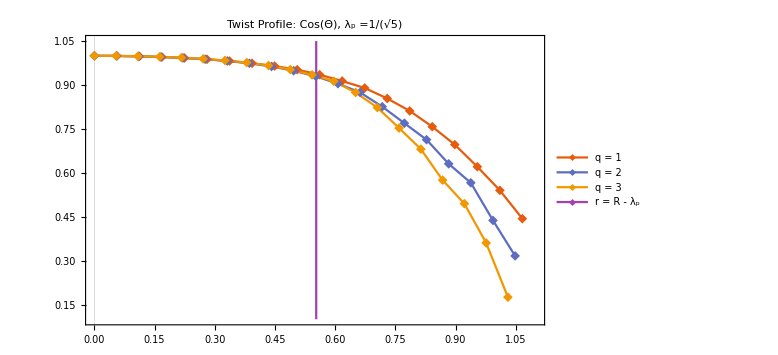

```mathematica
ListLinePlot[{NzC5q1,NzC5q2,NzC5q3,{{1-1/Sqrt[5],0},{1-1/Sqrt[5],1.5}}},PlotTheme->"Scientific", PlotLabel->"Twist Profile: Cos(Θ), λ_p =1/(√5)", PlotMarkers->{"◆", 10},PlotRange->{{0,1.1},{0.1,1.05}},PlotLegends->{"q = 1","q = 2","q = 3","r = R - λ_p"},ImageSize->Large]
```

### K=1, C = 15, q=1,2,3

```mathematica
NzC15q1={{0,0.999979},{0.0561338,0.999958},{0.112268,0.999871},{0.168401,0.999746},{0.224535,0.999541},{0.280669,0.999209},{0.336803,0.998696},{0.392937,0.99792},{0.44907,0.996691},{0.505204,0.995388},{0.561338,0.993556},{0.617472,0.991147},{0.673606,0.986533},{0.72974,0.979499},{0.785873,0.96682},{0.842007,0.950539},{0.898141,0.929908},{0.954275,0.901137},{1.01041,0.857466},{1.06654,0.782408}};
NzC15q2={{0,0.999964},{0.0561227,0.999915},{0.112245,0.999757},{0.168368,0.999497},{0.224491,0.999143},{0.280613,0.998521},{0.336736,0.997757},{0.392859,0.996642},{0.448981,0.995261},{0.505104,0.992851},{0.561227,0.989045},{0.617349,0.982284},{0.673472,0.97271},{0.729595,0.959118},{0.785717,0.937451},{0.84184,0.909527},{0.897963,0.874697},{0.954086,0.814598},{1.01021,0.746806},{1.06633,0.599501}};
NzC15q3={{0,0.999954},{0.056109,0.999891},{0.112218,0.999686},{0.168327,0.99935},{0.224436,0.998885},{0.280545,0.998071},{0.336654,0.997074},{0.392763,0.99562},{0.448872,0.993771},{0.504981,0.990402},{0.56109,0.985126},{0.617199,0.975956},{0.673308,0.96241},{0.729417,0.944959},{0.785526,0.915177},{0.841635,0.875923},{0.897744,0.823009},{0.953853,0.751821},{1.00996,0.6585},{1.06607,0.454088}};
```

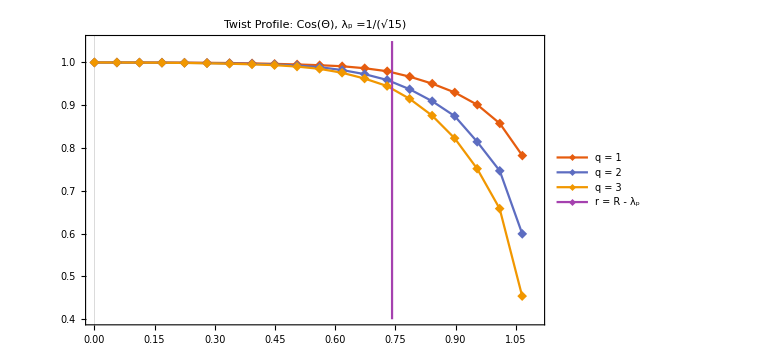

```mathematica
ListLinePlot[{NzC15q1,NzC15q2,NzC15q3,{{1-1/Sqrt[15],0},{1-1/Sqrt[15],1.5}}},PlotTheme->"Scientific", PlotLabel->"Twist Profile: Cos(Θ), λ_p =1/(√15)", PlotMarkers->{"◆", 10},PlotRange->{{0,1.1},{0.4,1.05}},PlotLegends->{"q = 1","q = 2","q = 3","r = R - λ_p"},ImageSize->Large]
```

### K = 1, C = 25, q = 1,2,3

```mathematica
NzC25q1={{0,0.999998},{0.0561299,0.999996},{0.11226,0.99999},{0.16839,0.999979},{0.224519,0.999959},{0.280649,0.999925},{0.336779,0.999866},{0.392909,0.999766},{0.449039,0.999614},{0.505169,0.999471},{0.561299,0.999159},{0.617429,0.998654},{0.673558,0.997446},{0.729688,0.995896},{0.785818,0.993257},{0.841948,0.98928},{0.898078,0.983116},{0.954208,0.965933},{1.01034,0.947508},{1.06647,0.903353}};
NzC25q2={{0,0.999996},{0.0561203,0.99999},{0.112241,0.999977},{0.168361,0.999946},{0.224481,0.999921},{0.280602,0.999846},{0.336722,0.999756},{0.392842,0.99956},{0.448963,0.999218},{0.505083,0.99857},{0.561203,0.997562},{0.617323,0.996511},{0.673444,0.993808},{0.729564,0.990158},{0.785684,0.982586},{0.841805,0.965707},{0.897925,0.950837},{0.954045,0.920065},{1.01017,0.864649},{1.06629,0.77411}};
NzC25q3={{0,0.999993},{0.0561162,0.999984},{0.112232,0.999961},{0.168349,0.999938},{0.224465,0.999869},{0.280581,0.999782},{0.336697,0.99959},{0.392813,0.999249},{0.44893,0.998633},{0.505046,0.997636},{0.561162,0.996599},{0.617278,0.994247},{0.673394,0.99062},{0.72951,0.983889},{0.785627,0.970588},{0.841743,0.952327},{0.897859,0.924803},{0.953975,0.859125},{1.01009,0.788427},{1.06621,0.612663}};
```

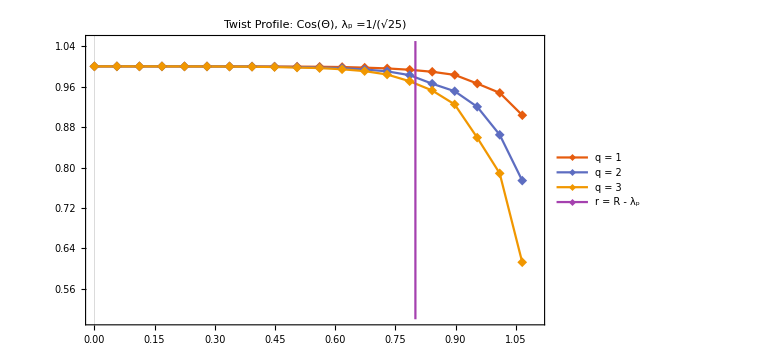

```mathematica
ListLinePlot[{NzC25q1,NzC25q2,NzC25q3,{{1-1/5,0},{1-1/5,1.5}}},PlotTheme->"Scientific", PlotLabel->"Twist Profile: Cos(Θ), λ_p =1/(√25)", PlotMarkers->{"◆", 10},PlotRange->{{0,1.1},{0.5,1.05}},PlotLegends->{"q = 1","q = 2","q = 3","r = R - λ_p"},ImageSize->Large ]
```

## Replicating Pelcovits and Meyer

```mathematica
fit[x_,θ0_] := -2ArcTan[Tan[-ArcSin[θ0]/2]Exp[-x]]
```

```mathematica
θR2={{2.04875,0.0254455},{2.04875,0.0254455},{1.84686,0.0523899},{1.84686,0.0523899},{1.63518,0.0824375},{1.63518,0.0824375},{1.43015,0.114879},{1.43015,0.114879},{1.16286,0.164347},{1.16286,0.164347},{0.923204,0.218011},{0.923204,0.218011},{0.688041,0.281106},{0.688041,0.281106},{0.483201,0.348239},{0.483201,0.348239},{0.231616,0.449201},{0.231616,0.449201},{0,0.56553},{0,0.56553}};
θ2Bob = {{1.9998,2.9034*10^(-05)},{1.9796,0.0029616},{1.9594,0.0058953},{1.9392,0.0088312},{1.919,0.01177},{1.8988,0.014714},{1.8786,0.017662},{1.8584,0.020617},{1.8382,0.02358},{1.818,0.026551},{1.7978,0.029532},{1.7776,0.032524},{1.7574,0.035528},{1.7372,0.038545},{1.717,0.041575},{1.6968,0.044621},{1.6766,0.047684},{1.6564,0.050763},{1.6362,0.053862},{1.616,0.05698},{1.5958,0.060118},{1.5756,0.063279},{1.5554,0.066463},{1.5352,0.069672},{1.515,0.072906},{1.4948,0.076167},{1.4746,0.079455},{1.4544,0.082773},{1.4342,0.086122},{1.414,0.089502},{1.3938,0.092915},{1.3736,0.096362},{1.3534,0.099844},{1.3332,0.10336},{1.313,0.10692},{1.2928,0.11052},{1.2726,0.11416},{1.2524,0.11784},{1.2322,0.12156},{1.212,0.12533},{1.1918,0.12914},{1.1716,0.13301},{1.1514,0.13692},{1.1312,0.14088},{1.111,0.1449},{1.0908,0.14897},{1.0706,0.15309},{1.0504,0.15727},{1.0302,0.16151},{1.01,0.16581},{0.9898,0.17017},{0.9696,0.1746},{0.9494,0.17909},{0.9292,0.18365},{0.909,0.18827},{0.8888,0.19297},{0.8686,0.19774},{0.8484,0.20258},{0.8282,0.2075},{0.808,0.21249},{0.7878,0.21757},{0.7676,0.22273},{0.7474,0.22797},{0.7272,0.23329},{0.707,0.23871},{0.6868,0.24421},{0.6666,0.2498},{0.6464,0.25549},{0.6262,0.26128},{0.606,0.26716},{0.5858,0.27314},{0.5656,0.27923},{0.5454,0.28542},{0.5252,0.29172},{0.505,0.29812},{0.4848,0.30464},{0.4646,0.31128},{0.4444,0.31803},{0.4242,0.3249},{0.404,0.33189},{0.3838,0.33901},{0.3636,0.34625},{0.3434,0.35362},{0.303,0.36876},{0.2828,0.37654},{0.2626,0.38446},{0.2424,0.39252},{0.2222,0.40072},{0.202,0.40908},{0.1818,0.41758},{0.1616,0.42624},{0.1414,0.43506},{0.101,0.45317},{0.0808,0.46248},{0.0606,0.47195},{0.0404,0.48159},{0.0202,0.49141},{0,0.50141}};

θR3={{3.36844,1.49012e-08},{3.05261,0.0173695},{3.05261,0.0173695},{2.73664,0.0361954},{2.73664,0.0361954},{2.38899,0.0604545},{2.38899,0.0604545},{2.03593,0.0914453},{2.03593,0.0914453},{1.67138,0.133605},{1.67138,0.133605},{1.67138,0.133605},{1.29716,0.192719},{1.29716,0.192719},{0.918062,0.276726},{0.918062,0.276726},{0.593765,0.377004},{0.593765,0.377004},{0.286557,0.501697},{0.286557,0.501697},{0,0.656716}};
θR4={{4.48928,4.21468e-08},{4.48928,4.21468e-08},{4.03247,0.0103129},{4.03247,0.0103129},{3.57446,0.0225152},{3.57446,0.0225152},{3.09612,0.039282},{3.09612,0.039282},{2.6116,0.0633545},{2.6116,0.0633545},{2.08609,0.102824},{2.08609,0.102824},{1.51137,0.1737},{1.51137,0.1737},{1.51137,0.1737},{0.993679,0.279463},{0.993679,0.279463},{0.628836,0.394302},{0.281776,0.541528},{0.281776,0.541528},{0,0.70304}};
θR5={{5.02879,0.00552656},{5.02879,0.00552656},{4.44366,0.0123131},{4.44366,0.0123131},{3.8264,0.0226718},{3.8264,0.0226718},{3.19788,0.0398826},{3.19788,0.0398826},{2.48136,0.0752426},{2.48136,0.0752426},{2.48136,0.0752426},{1.65889,0.155529},{1.65889,0.155529},{1.65889,0.155529},{1.05656,0.270936},{1.05656,0.270936},{0.322758,0.534642},{0.322758,0.534642},{0,0.720251}};
```

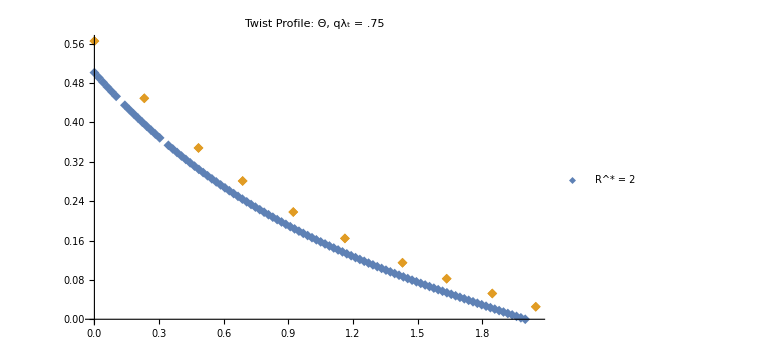

```mathematica
Show[ListPlot[{θ2Bob,θR2}, PlotMarkers->{"◆", 10},PlotLegends->{"R^* = 2"} ], PlotLabel->"Twist Profile: Θ, qλ_t = .75 ",ImageSize->Large ]
```

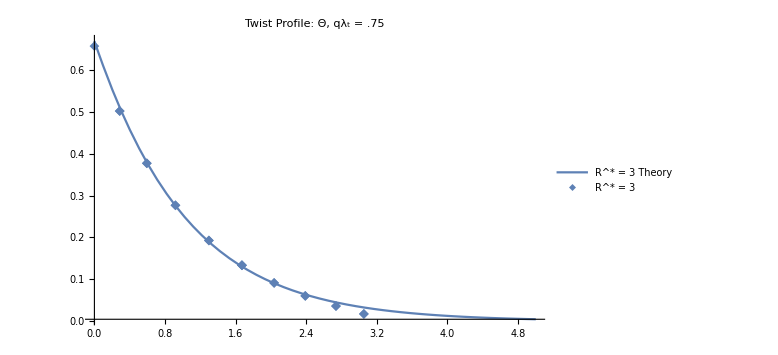

```mathematica
Show[Plot[fit[x,.62],{x,0,5},PlotRange -> Full ,PlotLegends->{"R^* = 3 Theory"}],ListPlot[θR3, PlotMarkers->{"◆", 10},PlotLegends->{"R^* = 3"} ], PlotLabel->"Twist Profile: Θ, qλ_t = .75 ",ImageSize->Large ]
```

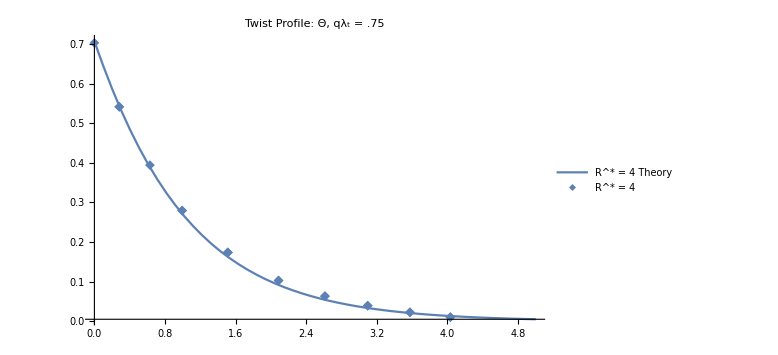

```mathematica
Show[Plot[fit[ x, .65],{x,0,5},PlotRange -> Full, PlotLegends->{"R^* = 4 Theory"} ],ListPlot[θR4, PlotMarkers->{"◆", 10},PlotLegends->{"R^* = 4"} ], PlotLabel->"Twist Profile: Θ, qλ_t = .75 ",ImageSize->Large ]
```

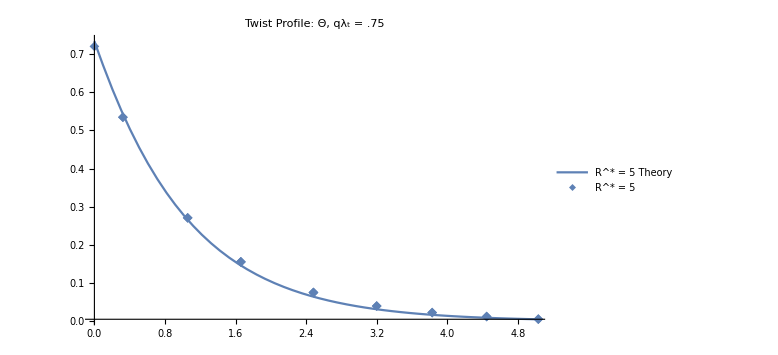

```mathematica
Show[Plot[fit[ x, .67],{x,0,5},PlotRange -> Full , PlotLegends->{"R^* = 5 Theory"}],ListPlot[θR5, PlotMarkers->{"◆", 10},PlotLegends->{"R^* = 5"} ], PlotLabel->"Twist Profile: Θ, qλ_t = .75 ",ImageSize->Large ]
```

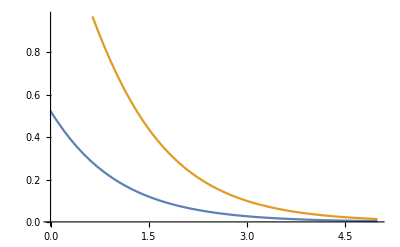

```mathematica
Plot[{fit[x, 0.5], fit[x, 1], fit[x, 1.5], fit[x, 2]}, {x, 0, 5}]
```

## Semi-Infinite Pi Wall: a thin perpendicular slice